## Phasenraum ohne Gaußverbreiterung

```mathematica
γ=1; B1=1; νres=1; c=0.1;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
Plot3D[MzNorm[Φ0,ν],{Φ0,0,20},{ν,-0,2},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->300,Boxed->False,PlotLabel->"Phasenraum ohne Gaußverbreiterung",AxesLabel->{"Normierte Einstrahlintensität","normierte Frequenz","Signal"},LabelStyle->Large]
```

-Graphics3D-

## Phasenraum mit Gaußverbreiterung

```mathematica
γ=1; B1=1; νres=1; c=0.05;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]:=NIntegrate[1/(1+u[ν]^2)(u[ν]^2+Cos[Φ √(1+u[ν]^2)])*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c Φ0)],{Φ,−Infinity,Infinity}];
Plot3D[MzNorm[Φ0,ν],{Φ0,0.1,20},{ν,1,1.5},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->50,Boxed->False,PlotLabel->"Phasenraum mit Gaußverbreiterung",AxesLabel->{"Drehwinkel","normierte Frequenz","Signal"},LabelStyle->Directive[Bold]]
```

## Experimentelle Daten Symmetrisieren

```mathematica
Dataminmax=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-minmax.dat", "Table"];
Dataminmax=Dataminmax[[14;;]]; k=0.85; l=1.14;
Datamaxmin=Transpose[{Dataminmax[[All,1]],(Dataminmax[[All,2]]*2/k/l+Dataminmax[[All,2]]^2/l/k^2)}];
Manipulate[ListPlot[Dataminmax, PlotRange->{-1,1}],{{k,0.85},0.001,2},{{l,1.14},1,1.5}]
ExSymData=(Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2)/.{k->0.85,l->1.14};
```

ListPlot::lpn: Dataminmax is not a list of numbers or pairs of numbers.

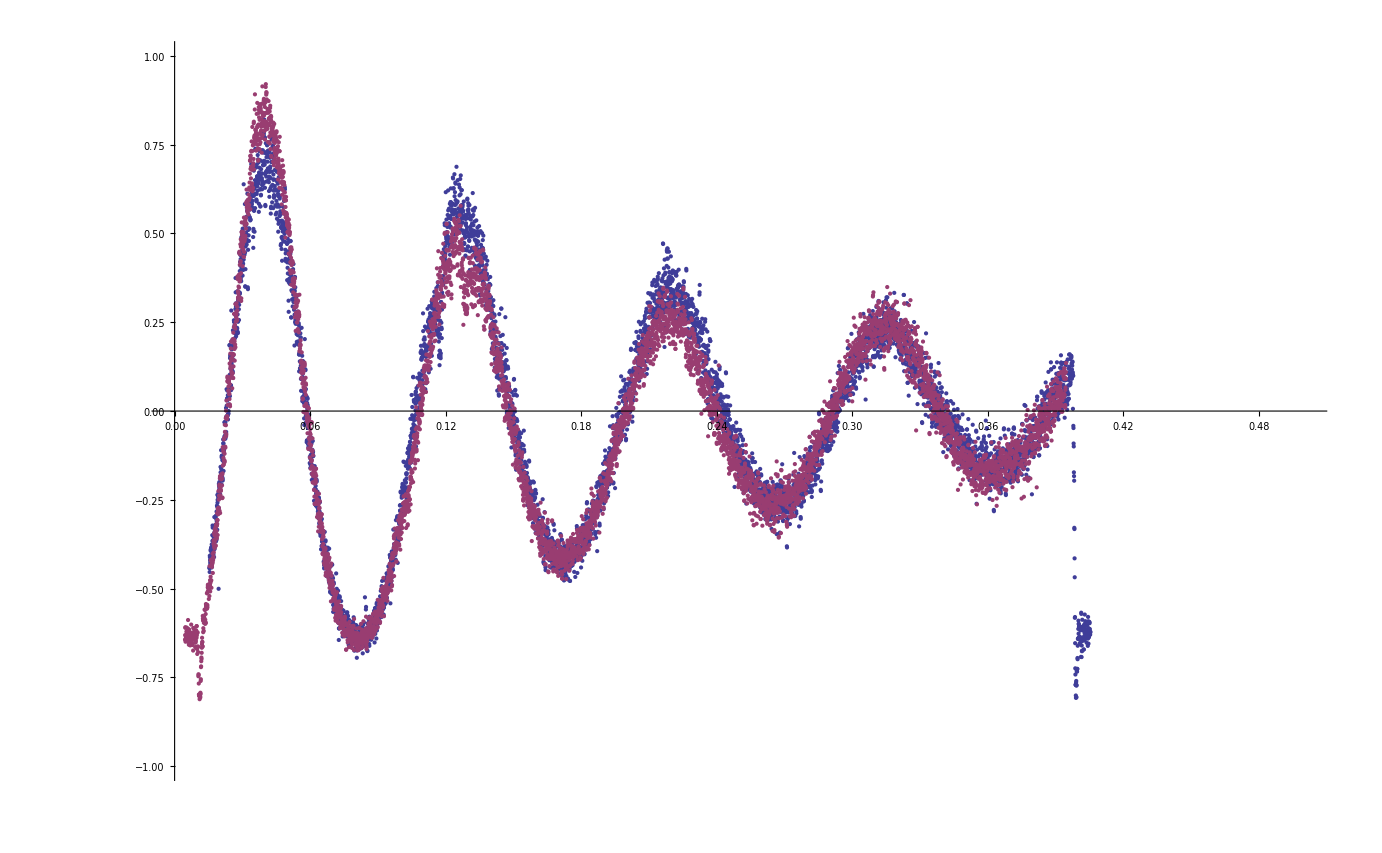

```mathematica
Dataxn=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-maxmin.dat", "Table"];
Datanx=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-minmax.dat", "Table"];
Dataxn=Dataxn[[14;;]]; 
Datanx=Datanx[[14;;]];
k=0.85; l=1.14;
Dataxn=Transpose[{Dataxn[[All,1]]+0.005395,(Dataxn[[All,2]]*2/k/l+Dataxn[[All,2]]^2/l/k^2)}];
Datanx=Transpose[{Datanx[[All,1]]-0.005395,(Datanx[[All,2]]*2/k/l+Datanx[[All,2]]^2/l/k^2)}];
ListPlot[{Dataxn,Datanx}, PlotRange->{{0,0.5},{-1,1}}]
ExSymData=Dataxn/0.95;
```

## Theorie nur auf der Resonanzfrequenz

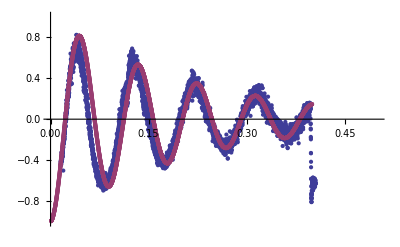

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.27; k=70;A=-1;
TheoData=Table[{B,A*MzNormSpinDreh[B*k,c]}, {B,0.001,0.4, 0.0001}];
ListPlot[{Dataxn,TheoData}, PlotRange->{{0,0.5},{-1,1}}]
```

```mathematica
Plot
```

## Experimentelle Daten

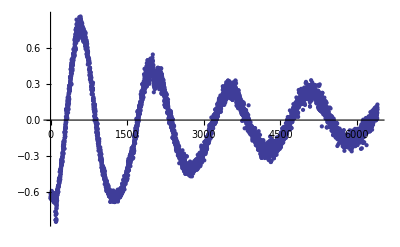

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
ExData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data]}];
ListPlot[ExData]
```

## Beide Funktionen

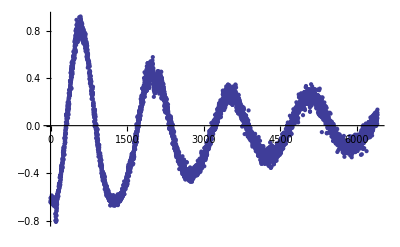

```mathematica
ListPlot[ExSymData]
```

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.25; γct=24000; j=1;shiftx=180;shifty=-0.01;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=ExSymData[[n]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1+shift,Length[Data]+shift,j}];
ListPlot[{ExSymData,ThData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

ListPlot::lpn: {{{0.405395, -0.623024}, {0.405334, -0.620985}, {0.405273, -0.629759}, {0.405212, -0.628755}, {0.405151, -0.613787}, {0.40509, -0.622005}, {0.405029, -0.597314}, {0.404968, -0.594461}, {0.404908, -0.630762}, « 33 », {0.402836, -0.625728}, {0.402775, -0.64588}, {0.402714, -0.644909}, {0.402653, -0.601215}, {0.402592, -0.634421}, {0.402531, -0.619622}, {0.40247, -0.671337}, {0.402409, -0.671337}, « 6351 »}, {}} is not a list of numbers or pairs of numbers.

ListPlot[«1»]

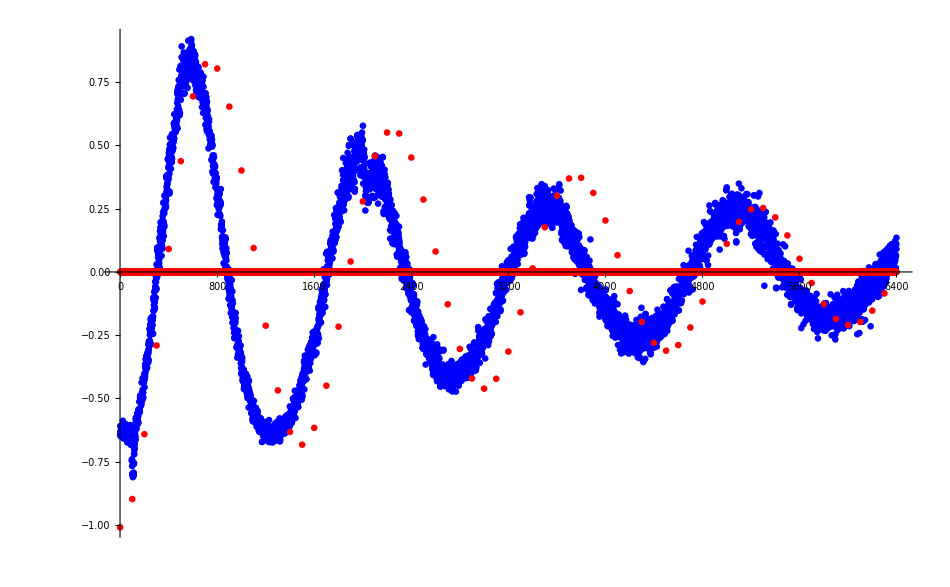

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.25; γct=240; j=100;shiftx=0;shifty=0;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=ExSymData[[n]],{n,1,Length[Data],j}];
Do[ThData[[Φ0]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1,Length[Data],j}];
ListPlot[{ExSymData,ThData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

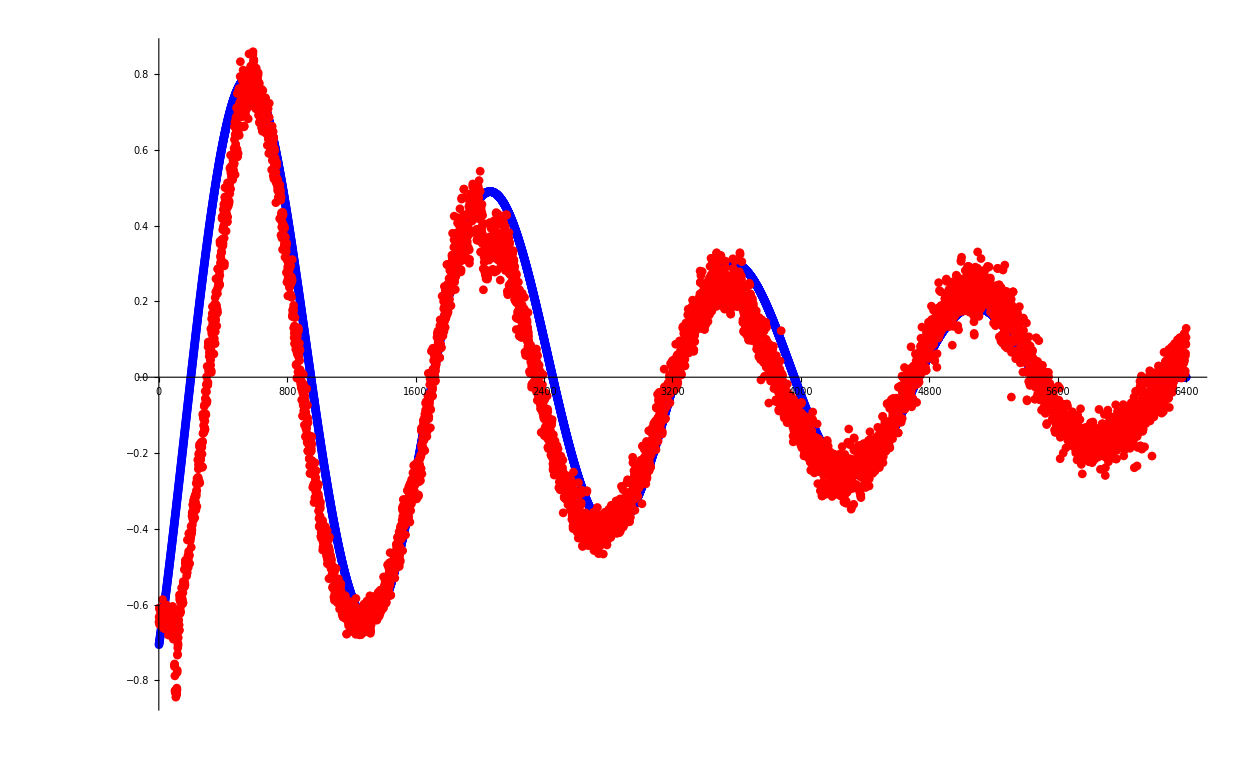

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.30; γct=240; j=1;shiftx=180;shifty=-0.01;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1+shift,Length[Data],j}];
ListPlot[{ThData,ExData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

## Daten Exportieren

```mathematica
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\ThData_von_Mathematica.dat",ThData]
```

D:\Git\F-Praktikum\NMR\Data-Plots\ThData_von_Mathematica.dat

## Andere Schnitte

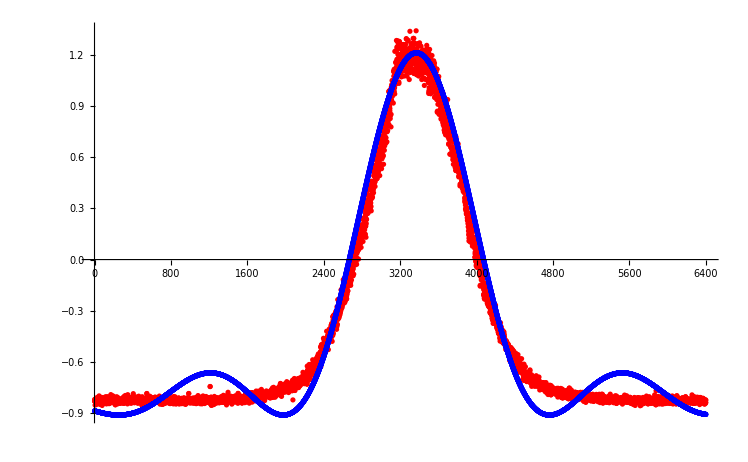

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-045mV-minmax-FM.dat", "Table"];
Data=Data[[14;;]];
k=0.85; l=1.14;
ExData=Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2;
γ=1; B1=1.5; νres=1; c=0.1;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
ThData=Table[0,{n,1,Length[Data]}];
Do[ThData[[ν]]=-MzNorm[π,ν/3370]*1.06+0.15,{ν,1,Length[Data]}];
ListPlot[{ExData,ThData},PlotStyle->{{Red,PointSize[0.005]},{Blue,PointSize[0.005]}}]
```

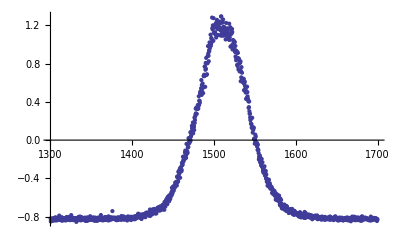

```mathematica
γB1=100;νres=1500;k=0.85; l=1.14;
DataExQuer=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-045mV-minmax-FM.dat", "Table"];
DataExQuer=DataExQuer[[14;;;;5]]; 
DataEQ=Transpose[{DataExQuer[[All,1]]+0.005395,(DataExQuer[[All,2]]*2/k/l+DataExQuer[[All,2]]^2/l/k^2)}];
u[ν_]:= 2 π (νres-ν)/γB1; MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
TheoData=Table[{ν,MzNorm[Pi,ν]}, {ν,1300,1400,1}];
ListPlot[ DataEQ]
```

```mathematica
k=0.85; l=1.14;
```

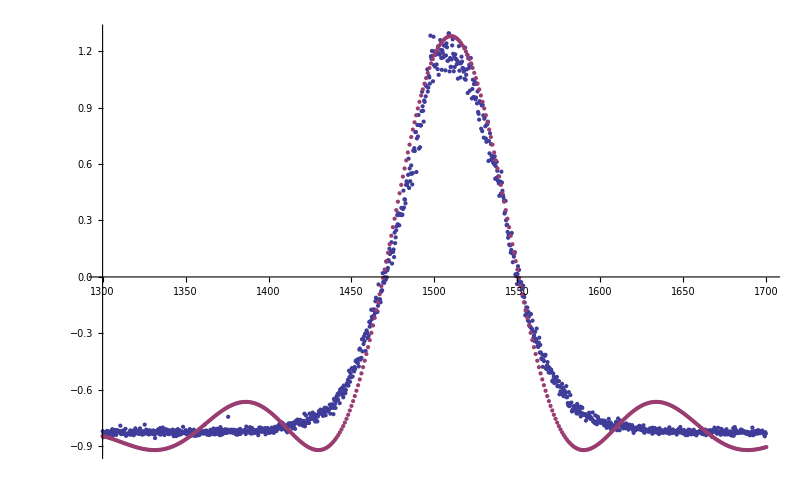

```mathematica
γB1=290;νres=1510;k=0.85; l=1.14;
DataExQuer=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-045mV-minmax-FM.dat", "Table"];
DataExQuer=DataExQuer[[14;;;;5]]; 
DataEQ=Transpose[{DataExQuer[[All,1]]+0.005395,(DataExQuer[[All,2]]*2/k/l+DataExQuer[[All,2]]^2/l/k^2)}];
u[ν_]:= 2 π (νres-ν)/γB1;
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
TheoData=Table[{ν,-1.1*MzNorm[2Pi,ν]+0.18}, {ν,1300,1700,1}];
ListPlot[{DataEQ,TheoData}]
```

```mathematica
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\180DrehungEx_von_Mathematica.dat",DataEQ];
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\180DrehungTheo_von_Mathematica.dat",TheoData];
```

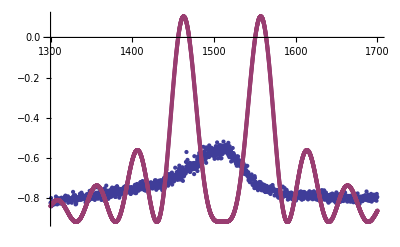

```mathematica
γB1=290;νres=1510;k=0.85; l=1.14;
DataExQuer=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-090mV-minmax-FM.dat", "Table"];
DataExQuer=DataExQuer[[14;;;;5]]; 
DataEQ=Transpose[{DataExQuer[[All,1]]+0.005395,(DataExQuer[[All,2]]*2/k/l+DataExQuer[[All,2]]^2/l/k^2)}];
u[ν_]:= 2 π (νres-ν)/γB1;
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
TheoData=Table[{ν,-1.1*MzNorm[2Pi,ν]+0.18}, {ν,1300,1700,0.1}];
ListPlot[{DataEQ,TheoData}]
```

```mathematica
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\360DrehungEx_von_Mathematica.dat",DataEQ];
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\360DrehungTheo_von_Mathematica.dat",TheoData];
```

```mathematica
Dataxn=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-maxmin.dat", "Table"];
Datanx=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-minmax.dat", "Table"];
Dataxn=Dataxn[[14;;]]; 
Datanx=Datanx[[14;;]];
k=0.85; l=1.14;
Dataxn=Transpose[{Dataxn[[All,1]]+0.005395,(Dataxn[[All,2]]*2/k/l+Dataxn[[All,2]]^2/l/k^2)}];
Datanx=Transpose[{Datanx[[All,1]]-0.005395,(Datanx[[All,2]]*2/k/l+Datanx[[All,2]]^2/l/k^2)}];
ListPlot[{Dataxn,Datanx}, PlotRange->{{0,0.5},{-1,1}}]
ExSymData=Dataxn/0.95;
```

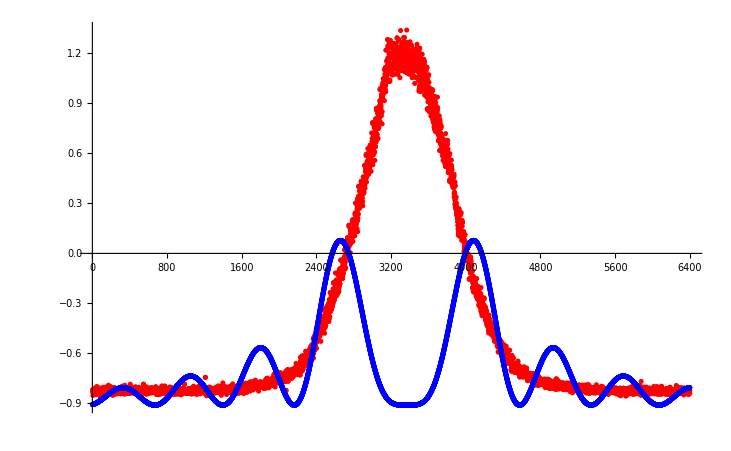

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-045mV-minmax-FM.dat", "Table"];
Data=Data[[14;;]];
k=0.85; l=1.14;
ExData=Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2;
γ=1; B1=1.3; νres=1; c=0.1;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
ThData=Table[0,{n,1,Length[Data]}];
Do[ThData[[ν]]=-MzNorm[2π,ν/3370]*1.06+0.15,{ν,1,Length[Data]}];
ListPlot[{ExData,ThData},PlotStyle->{{Red,PointSize[0.005]},{Blue,PointSize[0.005]}}]
```

```mathematica
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\EDataxn_von_Mathematica.dat",Dataxn]
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\TheoData_von_Mathematica.dat",TheoData]
```

D:\Git\F-Praktikum\NMR\Data-Plots\EDataxn_von_Mathematica.dat

D:\Git\F-Praktikum\NMR\Data-Plots\TheoData_von_Mathematica.dat

```mathematica
Integrate[1/(1+l^2)^(3/2),{l,-Infinity, Infinity}]
```

2

```mathematica
N[Integrate[1/(1+l^2)^(3/2),{l,-4.6,4.6}]]
```

1.95435

```mathematica
Abweichung=%/2
```

0.977176